# Supplementary Materials for The Meaning and Measure of Heterogeneity

Abraham Nunes (nunes@dal.ca), Thomas Trappenberg, and Martin Alda
Dalhousie University, Halifax, Nova Scotia, Canada

## A. Mathematical Details

## A.1 Proposed Heterogeneity Axioms

AXIOM 1 (NON-NEGATIVITY)
The heterogeneity measure h(y) is strictly positive ∀y ∈𝒴⊆ℝ_(≥ 0)^n \ {∅}.

AXIOM 2 (NULL EMPTY SET)
The heterogeneity measure h:𝒴→ ℝ_(≥0) equals 0 iff 𝒴=∅.

AXIOM 3 (SYMMETRY)
Given an abundance distribution y=(y_i)_(i=1)^n∈𝒴⊆ℝ_(≥0)^n and a permutation function σ:ℤ_+→ℤ_+, the heterogeneity measure h:𝒴→ ℝ_(≥0) satisfies

			h({y_1, y_2, …, y_n})=h({y_(σ(1)), y_(σ(2)), …, y_(σ(n))}).

AXIOM 4 (CONTINUITY AND DIFFERENTIABILITY)
The heterogeneity measure h:𝒴→ ℝ_(≥0) is a continuous and differentiable function ∀y∈𝒴.

AXIOM 5a (EXTENSIVITY OR MONOTONICITY TO SET SIZE)
Given a family of distributions y(n)=(y_i)_(i=1)^n with a constant level of inequality for all n∈ℕ_+, the heterogeneity measure h must satisfy
	
		h(y(n + δ)) > h(y(n))  ∀δ∈ℕ_+

AXIOM 5b (NON-EXTENSIVITY OR INVARIANCE TO SET SIZE)
Given a family of distributions y(n)=(y_i)_(i=1)^n with a constant level of inequality for all n∈ℕ_+, the heterogeneity measure h must satisfy
	
		h(y(n + δ)) = h(y(n))  ∀δ∈ℕ_+

Remark. Extensivity is typically desirable for heterogeneity measures corresponding to set size. Measures that are specifically focused on inequality generally require non-extensivity.

AXIOM 6 (PRINCIPLE OF TRANSFERS) 
Given an abundance vector  y=(y_i)_(i=1)^n, if we define a new vector y' by the following transfer of some small amount of abundance ,

	y'_k=Piecewise[{{y_k-ϵ, k=j}, {y_k+ϵ, k=i}, {y_k, k≠i∧k≠j}}]

where y_j>y_i then heterogeneity must increase, with a maximal value attained iff y_i=y_j.

AXIOM 7 (THE REPLICATION PRINCIPLE)
We are given n_s∈ℕ_(≥2) systems, with respective distributions y_i ∀i∈{1, 2, …, n_s}, whose domains of support are non-overlapping, but whose heterogeneities are equal: 

		h(y_i)=h(y_j) ∀(i,j)∈{1,2,…, n_s}

Letting ȳ be the abundance distribution on the pooled n_s systems, the replication principle states that

		h(ȳ)=n_s h(y_i)  ∀i∈{1,2,…, n_s}.

AXIOM 8 (DECOMPOSABILITY)
Given a system 𝒳 with abundance distribution p that is a composition of subsystems 𝒳^(1),𝒳^(2),…, 𝒳^(K) with corresponding abundance distributions y_1,y_2,…,y_n, then we define the heterogeneity of the composite system—also known as the total heterogeneity or γ-heterogeneity—as h^γ(ȳ), although for brevity we will simply denote it as h^γ. The component of total heterogeneity due to within-group factors is also known as the α-heterogeneity, and is denoted as h^α. Finally, the component of heterogeneity due to between-group differences is denoted as h^β and is known as the β-heterogeneity. The heterogeneity measure h is decomposable if (Jost, 2007): 

A. There exists a deterministic function Ξ such that h^γ=Ξ(h^α, h^β)
B. The within and between-group components are independent: h^α⫫ h^β
C. The within-group heterogeneity is a lower bound on total heterogeneity: h^α≤ h^γ
D. The within-group and between-group components have the same units

AXIOM 9 (SCALE INVARIANCE) 
Given an abundance vector y=(y_i)_(i=1)^n and a positive scalar k∈ℝ_+, h(k y)=h(y)

## A.2. Numbers Equivalent

Consider a set 𝒳 with probability (abundance) distribution p = (p_i)_(i=1)^(n_c^(p)) and heterogeneity

Π_q[p]=(∑_(i=1)^(n_c^(p)) p_i^q)^(1/(1-q))

Given a second set 𝒳' with a uniform distribution u_j=1/n_c^(u) ∀j∈{1, 2, …, n_c^(u)} whose heterogeneity is such that Π_q[p]=Π_q[u], we can easily see that

```mathematica
TraditionalForm@PowerExpand@ReplaceAll[{Subscript[u, j]->1/Subscript[n, c]^(u)}][(∑_(i=1)^(Subscript[n, c]^(p)) Subscript[p, i]^q)^(1/(1-q))==(∑_(j=1)^(Subscript[n, c]^(u)) Subscript[u, j]^q)^(1/(1-q))]
```

(∑_(i=1)^(n_c^p) p_i^q)^(1/(1-q))==n_c^(-((q-1) u)/(1-q))

```mathematica
TraditionalForm@FullSimplify[%]
```

n_c^u==(∑_(i=1)^(n_c^p) p_i^q)^(1/(1-q))

which shows that the heterogeneity of 𝒳 is the number of partitions n_c^(u) in an equally heterogeneous set 𝒳' with uniform abundance distribution.

## A.3. Entropies and the Replication Principle

PROPOSITION A1. Entropies derived from Tsallis’ form fail to satisfy the replication principle.

Proof. Assume the total number of partitions in a system composed of Msubsystems is  n=∑_(i=1)^M n_i, where n_i is the number of partitions in the i’th sample. The probability distribution for system i is p_i=(p_(i,1), p_(i,2), …, p_(i,n_i)). Recall that the domains of support for p_1, p_2,…, p_M are disjoint. The Tsallis entropy of a single system is

```mathematica
Subscript[T, q][Subscript[p, i]] = 1/(q-1)(1-∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q)
```

(1-∑_(j=1)^n_i p_(i,j)^q)/(-1+q)

and the Tsallis entropy of the pooled system, whose probability distribution is p̄, is as follows:

```mathematica
Subscript[T, q][p̄] = 1/(q-1)(1-∑_(k=1)^n Subscript[p̄, k]^q)
```

(1-∑_(k=1)^n (p̄)_k^q)/(-1+q)

Since the domains for each of the M subsystems is disjoint, we have that

P=(p_(1,1) | p_(1,2) | ⋯ | p_(1,n_1) | 0 | 0 | 0 | 0 | ⋯ | 0 | 0 | 0 | 0 | ⋯ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | p_(2,1) | p_(2,2) | … | p_(2 n_2) | ⋯ | ⋮ | ⋮ | ⋮ | ⋮ | ⋯ | ⋮ | ⋮ | ⋮ | ⋮
⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋱ | ⋮ | ⋮ | ⋮ | ⋮ | ⋯ | ⋮ | ⋮ | ⋮ | ⋮
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⋯ | p_(i,1) | p_(i,2) | … | p_(i,n_i) | ⋯ | 0 | 0 | 0 | 0
⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋯ | ⋮ | ⋮ | ⋮ | ⋮ | ⋱ | ⋮ | ⋮ | ⋮ | ⋮
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⋯ | 0 | 0 | 0 | 0 | ⋯ | p_(M,1) | p_(M,2) | … | p_(M,n_M))

and

p̄=1/M(p_(1,1) | p_(1,2) | ⋯ | p_(1,n_1) | p_(2,1) | p_(2,2) | … | p_(2 n_2) | ⋯ | p_(i,1) | p_(i,2) | … | p_(i,n_i) | ⋯ | p_(M,1) | p_(M,2) | … | p_(M,n_M))

Substituting (3) into the Tsallis entropy yields the following expression:

```mathematica
Subscript[T, q][p̄] = PowerExpand[Subscript[T, q][p̄]/.{∑_(k=1)^n Subscript[p̄, k]^q ->∑_(i=1)^M ∑_(j=1)^Subscript[n, i] (Subscript[p, i,j]/M)^q}]
```

(1-∑_(i=1)^M ∑_(j=1)^n_i M^-q p_(i,j)^q)/(-1+q)

Rearranging terms,

```mathematica
num = Numerator[Subscript[T, q][p̄]]/.{ 
	1-∑_(v1_=l1_)^h1_ ∑_(v2_=l2_)^h2_ r_ q_/;FreeQ[r, v1]∧FreeQ[r, v2]:> 1- r∑_(v1=l1)^h1 ∑_(v2=l2)^h2 q}
Subscript[T, q][p̄] = num/Denominator[Subscript[T, q][p̄]];
```

1-M^-q ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q

we recall that ∑_(j=1)^n_i p_(i,j)^q=∑_(j=1)^n_k p_(k,j)^q for all i,k. Letting λ_i=∑_(j=1)^n_i p_(i,j)^q,  T_q[p̄] simplifies to

```mathematica
Subscript[T, q][p̄] = ReplaceAll[{∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q -> M Subscript[λ, i]}][Subscript[T, q][p̄]]
```

(1-M^(1-q) λ_i)/(-1+q)

and T_q[p_i] simplifies to the following.

```mathematica
Subscript[T, q][Subscript[p, i]] = ReplaceAll[{∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q -> Subscript[λ, i]}][Subscript[T, q][Subscript[p, i]]]
```

(1-λ_i)/(-1+q)

The replication principle states that the following equality must hold: T_q[p̄]=M T_q[p_i]. We conclude the proof by showing that it does not. Note that λ_i=∑_(j=1)^n_i p_(i,j)^q.

```mathematica
pa1eq = ApplySides[ExpandAll[#×(q-1)]&, Subscript[T, q][p̄]== M Subscript[T, q][Subscript[p, i]]]
```

1-M^(1-q) λ_i==M-M λ_i

```mathematica
pa1eq = ApplySides[(#-1)/(M-M^(1-q))&,FullSimplify@pa1eq]
```

λ_i==(-1+M)/(M-M^(1-q))

This equality holds only at q=1, which is irrelevant since T_q[p] is undefined at q=1 (we will prove this in the limiting case of q→1 below). Showing that the above equality is not generally true is easy under a counterexample. Substituting λ_i→(p_(i,n_i)-ϵ)^q+(p_(i,n_i-1)+ϵ)^q+∑_(j=1)^(n_i-2) p_(i,j)^q and differentiating with respect to ϵ, we obtain our result.

```mathematica
pa1eq =pa1eq/.Subscript[λ, i]->(Subscript[p, i,Subscript[n, i]]-ϵ)^q+(Subscript[p, i,Subscript[n, i]-1]+ϵ)^q+∑_(j=1)^(Subscript[n, i]-2) Subscript[p, i,j]^q
```

(ϵ+p_(i,-1+n_i))^q+(-ϵ+p_(i,n_i))^q+∑_(j=1)^(-2+n_i) p_(i,j)^q==(-1+M)/(M-M^(1-q))

```mathematica
pa1eq = ApplySides[D[#, M]&, pa1eq]
```

0==1/(M-M^(1-q))-((-1+M) (1-M^-q (1-q)))/((M-M^(1-q))^2)

```mathematica
pa1eq = ExpandAll@ApplySides[
	(#+((-1+M) (1-M^-q (1-q)))/((M-M^(1-q))^2))(M-M^(1-q))^2& , pa1eq]
```

-1+M-M^(1-q)+M^-q+M^(1-q) q-M^-q q==M-M^(1-q)

```mathematica
pa1eq = ApplySides[# -M+M^(1-q)+M^-q q-M^-q &, pa1eq]
```

-1+M^(1-q) q==-M^-q+M^-q q

```mathematica
pa1eq = ApplySides[#/(-1+M^q+q-M q) & , FullSimplify@pa1eq]
```

M^-q==0

```mathematica
FullSimplify[pa1eq, Assumptions->{M≥1, q>0}]
```

False

Thus, for q≠1, the Tsallis family of entropies does not satisfy the replication principle. We now show the q→1 case. We use L’Hopital’s rule to obtain T_1[p]:

```mathematica
Subscript[T, 1][Subscript[p, i]] = Limit[D[1-∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q, q]/D[q-1, q], q->1] /. lim_(e_->a_) -∑_(v_=l_)^u_ Log[x_] x_^e_ :>-∑_(v=l)^u lim_(e->a) (Log[x] x^e)
```

-∑_(j=1)^n_i Log[p_(i,j)] p_(i,j)

and similarly for T_1[p̄]

```mathematica
Subscript[T, 1][p̄] = Limit[D[1-∑_(i=1)^M ∑_(j=1)^Subscript[n, i] (Subscript[p, i,j]/M)^q, q]/D[q-1, q], q->1] /.{
			lim_(e_->a_) -∑_(v1_=l1_)^u1_ ∑_(v_=l_)^u_ Log[x_] x_^e_ :>-∑_(v1=l1)^u1 ∑_(v=l)^u lim_(e->a) (Log[x] x^e) }
```

-∑_(i=1)^M ∑_(j=1)^n_i (Log[(p_(i,j))/M] p_(i,j))/M

```mathematica
Subscript[T, 1][p̄] = Subscript[T, 1][p̄]/. {-∑_(i=1)^M ∑_(j=1)^Subscript[n, i] (Log[Subscript[p, i,j]/M] Subscript[p, i,j])/M->-1/M∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Log[Subscript[p, i,j]/M] Subscript[p, i,j]}
```

-(∑_(i=1)^M ∑_(j=1)^n_i Log[(p_(i,j))/M] p_(i,j))/M

```mathematica
pa1eq2 = M Subscript[T, 1][p̄] == M^2 Subscript[T, 1][Subscript[p, i]]
```

-∑_(i=1)^M ∑_(j=1)^n_i Log[(p_(i,j))/M] p_(i,j)==-M^2 ∑_(j=1)^n_i Log[p_(i,j)] p_(i,j)

```mathematica
pa1eq2 = pa1eq2 /. -∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Log[Subscript[p, i,j]/M] Subscript[p, i,j] -> -∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j] Log[Subscript[p, i,j]]-Log[M]∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j]
```

-Log[M] ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)-∑_(i=1)^M ∑_(j=1)^n_i Log[p_(i,j)] p_(i,j)==-M^2 ∑_(j=1)^n_i Log[p_(i,j)] p_(i,j)

Since ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)=M and letting ∑_(j=1)^n_i Log[p_(i,j)] p_(i,j)=λ_i,

```mathematica
pa1eq2 = pa1eq2 /. {
	∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j] -> M,
	∑_(j=1)^Subscript[n, i] Log[Subscript[p, i,j]] Subscript[p, i,j]->Subscript[λ, i],
	∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Log[Subscript[p, i,j]] Subscript[p, i,j]->M Subscript[λ, i]
}
```

-M Log[M]-M λ_i==-M^2 λ_i

```mathematica
Flatten@Solve[ApplySides[FullSimplify[#/M]&,pa1eq2], Subscript[λ, i]]
```

{λ_i→Log[M]/(-1+M)}

Since the LHS is variable and the RHS is constant, this equality cannot hold.

□

## A.4. Properties of the Rényi Heterogeneity

The Rényi heterogeneity is defined as

```mathematica
Subscript[Π, q][p] = (∑_(i=1)^m Subscript[p, i]^q)^(1/(1-q));
```

```mathematica
Subscript[Π, 0][p]=∑_(i=1)^m Subscript[p, i]>0;
```

```mathematica
Subscript[Π, 1][p]=ⅇ^(-∑_(i=1)^m Subscript[p, i] Log[Subscript[p, i]]);
```

```mathematica
Subscript[Π, ∞][p]=1/Max[p];
```

PROPOSITION A2. The Rényi heterogeneity is non-negative.

The proof is trivial since p_i≥0  ∀i∈{1,2,…, n}.

PROPOSITION A3. The Rényi heterogeneity is symmetric.

The proof is trivial by the commutative properties of addition, maximum, and the indicator function.

PROPOSITION A4. The Rényi heterogeneity is continuous and differentiable with respect to the probability distribution p.

Proof. The Rényi heterogeneity can be viewed as a composition of continuous functions, and is therefore continuous for 0<p_i≤1. At q≠1:

```mathematica
f[x_] := Subscript[x, i]^q
g[x_, v_:i,l_:1,u_:m] :=∑_(v=l)^u x
h[x_] := x^(1/(1-q)) 
h@g@f[p]
```

(∑_(i=1)^m p_i^q)^(1/(1-q))

As q→1, we have the following:

```mathematica
Ι[x_]:= -Log[Subscript[x, i]]
𝔼[x_, v_:i,l_:1,u_:m][y_]:=∑_(v=l)^u Subscript[x, i] y
Exp@𝔼[p]@Ι[p]
```

ⅇ^(∑_(i=1)^m -Log[p_i] p_i)

The derivative of the Rényi heterogeneity in terms of it’s component functions is

```mathematica
ClearAll[f,g,h]
D[h@g@f[x], x]
```

f'[x] g'[f[x]] h'[g[f[x]]]

We can verify that the component derivatives exist so long as q≠1,

```mathematica
D[g[x]^(1/(1-q)), g[x]]//FullSimplify
```

g[x]^(-q/(-1+q))/(1-q)

```mathematica
FullSimplify[D[∑_(i=1)^m f[Subscript[x, i]], f[Subscript[x, i]]], Assumptions->{1≤i≤m, i∈Integers}]
```

1

```mathematica
FullSimplify[D[f[Subscript[x, i]], Subscript[x, i]], Assumptions->{1≤i≤m}]
```

f'[x_i]

although one could easily show that the derivatives exist for the q→1 limit.  The derivative of Rényi heterogeneity with respect to p_k therefore exists by the chain rule.

(∂Π_q)/(∂p_k)=(∂Π_q)/(∂h)(∂h)/(∂g)(∂g)/(∂f)(∂f)/(∂p_k)

□

PROPOSITION A5. The Rényi heterogeneity is monotonic to set size.

Proof. For p=(p_i)_(i=1)^n, recall that Π_0[p]=n. One can show that the derivative of the Rényi entropy with respect to q is proportional to the negative Kullback-Leibler divergence ∑_(i=1)^m z_i Log[z_i/p_i], where z_i=p_i^q/∑_(i=1)^m p_i^q:

```mathematica
pa5expr = -D[Log[Subscript[Π, q][p]], q]
```

-Log[∑_(i=1)^m p_i^q]/(1-q)^2-(∑_(i=1)^m Log[p_i] p_i^q)/((1-q) ∑_(i=1)^m p_i^q)

Letting z_i=p_i^q/∑_(i=1)^m p_i^q and substituting, we see that

```mathematica
pa5expr = pa5expr/.{
	(∑_(i=1)^m Log[Subscript[p, i]] Subscript[p, i]^q)/((1-q) ∑_(i=1)^m Subscript[p, i]^q)-> (∑_(i=1)^m Subscript[z, i] Log[Subscript[p, i]])/(1-q)}
```

-Log[∑_(i=1)^m p_i^q]/(1-q)^2-(∑_(i=1)^m Log[p_i] z_i)/(1-q)

```mathematica
pa5expr = PowerExpand@Together@pa5expr /. {
	Log[∑_(i=1)^m Subscript[p, i]^q]->q∑_(i=1)^m Subscript[z, i] Log[Subscript[p, i]]-∑_(i=1)^m Subscript[z, i] Log[Subscript[z, i]]}/. {
	-∑_(i=1)^m Log[Subscript[p, i]] Subscript[z, i]+∑_(i=1)^m Log[Subscript[z, i]] Subscript[z, i]->∑_(i=1)^m Subscript[z, i] Log[Subscript[z, i]/Subscript[p, i]]}
```

(∑_(i=1)^m Log[z_i/p_i] z_i)/(-1+q)^2

This means that Π_q[p] is nondecreasing with respect to q, and thus (Π_q[p]/Π_0[p])≤1. Now define a family of distributions p(n)=(p_i)_(i=1)^n with a constant level of evenness, Π_q[p(n)]/Π_0[p(n)]. Therefore,

```mathematica
pa5eq = (Subscript[Π, q][p[n]])/(Subscript[Π, 0][p[n]])==(Subscript[Π, q][p[n+1]])/(Subscript[Π, 0][p[n+1]])
```

Π_q[p[n]]/Π_0[p[n]]==Π_q[p[1+n]]/Π_0[p[1+n]]

```mathematica
pa5eq = pa5eq/.{Subscript[Π, 0][p[n]]->n, Subscript[Π, 0][p[n+1]]->n+1}
```

Π_q[p[n]]/n==Π_q[p[1+n]]/(1+n)

```mathematica
ApplySides[#/Subscript[Π, q][p[n]]&, ApplySides[# (n+1) &, pa5eq]]
```

(1+n)/n==Π_q[p[1+n]]/Π_q[p[n]]

□

PROPOSITION A6. The Rényi heterogeneity obeys the principle of transfers.

Proof. For some small  ϵ transfer from p_n to p_(n-1), when before the transfer p_n>p_(n-1), the Rényi heterogeneity is

```mathematica
Subscript[Π, q][p'] = ((Subscript[p, n-1]+ϵ)^q + (Subscript[p, n]-ϵ)^q + ∑_(i=1)^(n-2) Subscript[p, i]^q)^(1/(1-q));
```

Differentiating with respect to ϵ  and solving for ∂_ϵ Π_q[p'] gives

```mathematica
SubStar[ϵ]= Extract[Solve[D[Subscript[Π, q][p'], ϵ]==0, ϵ], {1, 1, 2}]
```

1/2 (-p_(-1+n)+p_n)

which is a transfer that would set p_n=p_(n-1). We can show that Π_q[p'] is maximized at ϵ_* by demonstrating that Π_q[p'] has constant negative curvature.

```mathematica
pa6curv = FullSimplify[D[Subscript[Π, q][p'], {ϵ, 2}]/.ϵ->SubStar[ϵ]];
pa6ineq = pa6curv ≤ 0
```

-(8 q (p_(-1+n)+p_n)^(-2+q) (2^(1-q) (p_(-1+n)+p_n)^q+∑_(i=1)^(-2+n) p_i^q)^(1/(1-q)))/(2 (p_(-1+n)+p_n)^q+2^q ∑_(i=1)^(-2+n) p_i^q)≤0

```mathematica
pa6ineq = ApplySides[# Denominator[pa6curv]&, pa6ineq];
pa6ineq = ApplySides[# / Extract[pa6ineq, {1,4}]&, pa6ineq]
```

-8 q (p_(-1+n)+p_n)^q≤0

Since  (p_(-1+n)+p_n)>0 and q>0, the inequality is true.

□

PROPOSITION A7. The Rényi heterogeneity obeys the replication principle.

Proof. The Rényi heterogeneity for a single subsystem is

```mathematica
Subscript[Π, q][Subscript[p, i]] = (∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q)^(1/(1-q));
```

and for the pooled system is

```mathematica
Subscript[Π, q][p̄] = (∑_(i=1)^M ∑_(j=1)^Subscript[n, i] (Subscript[p, i,j]/M)^q)^(1/(1-q));
```

The replication principle states that

```mathematica
pa7eq = Subscript[Π, q][p̄] == M Subscript[Π, q][Subscript[p, i]]
```

(∑_(i=1)^M ∑_(j=1)^n_i ((p_(i,j))/M)^q)^(1/(1-q))==M (∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))

```mathematica
pa7eq = ApplySides[PowerExpand, pa7eq] /.{
	(∑_(i=1)^M ∑_(j=1)^Subscript[n, i] M^-q Subscript[p, i,j]^q)^(1/(1-q)) -> (M^-q∑_(i=1)^M ∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q)^(1/(1-q))}
```

(M^-q ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))==M (∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))

Letting λ_i=∑_(j=1)^n_i p_(i,j)^q:

```mathematica
pa7eq = pa7eq /.{∑_(j=1)^Subscript[n, i] Subscript[p, i,j]^q->Subscript[λ, i]}
```

(M^-q ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))==M λ_i^(1/(1-q))

Finally, since λ_i=λ_k ∀i,k∈{1,2,…, M},

```mathematica
pa7eq = pa7eq /.{(M^-q ∑_(i=1)^M Subscript[λ, i])^(1/(1-q))->(M^(1-q)Subscript[λ, i])^(1/(1-q))}
```

(M^-q ∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))==M λ_i^(1/(1-q))

```mathematica
PowerExpand@pa7eq
```

M^(-q/(1-q)) (∑_(i=1)^M ∑_(j=1)^n_i p_(i,j)^q)^(1/(1-q))==M λ_i^(1/(1-q))

□

PROPOSITION A8. The Rényi heterogeneity has a multiplicative decomposition.

The proof can be found in Jost (2007).

PROPOSITION A9. The Rényi heterogeneity is scale invariant.

The proof is trivial since the Rényi heterogeneity operates on probability distributions.

## A.5. Shannon Entropy and Typical Set Size

Given a total of n observations from a system with m classes, let the observed abundance distribution over classes be denoted y=(y_1, y_2, …, y_m). The effective number of typical such samples of size n is

```mathematica
S =(n!)/(∏_(i=1)^m (Subscript[p, i]!))
```

(n!)/(∏_(i=1)^m p_i!)

Taking logs of both sides, we have the following.

```mathematica
logS = PowerExpand@Log[S] /.Log[∏_(v_=l_)^u_ x_]:>∑_(v=l)^u Log[x]
```

Log[n!]-∑_(i=1)^m Log[p_i!]

Now we can employ Stirling’s approximation:

```mathematica
stirlingapprox[x_] = {Log[x!]-> x Log[x]-x};
logS = logS /. Flatten[{stirlingapprox[n], stirlingapprox[Subscript[p, i]]}];
logS = logS /.∑_(v_=l_)^u_ (-a_ + b_):>-∑_(v=l)^u a + ∑_(v=l)^u b
```

-n+n Log[n]+∑_(i=1)^m p_i-∑_(i=1)^m Log[p_i] p_i

```mathematica
logS = logS/. ∑_(i=1)^m Subscript[p, i]->n /.n Log[n]->∑_(i=1)^m Subscript[p, i] Log[n]
```

∑_(i=1)^m Log[n] p_i-∑_(i=1)^m Log[p_i] p_i

```mathematica
logS = logS/. ∑_(v_=l_)^u_ Log[b_] a_-∑_(v_=l_)^u_ Log[a_] a_ :> -∑_(i=1)^m a Log[a/b]
```

-∑_(i=1)^m Log[p_i/n] p_i

When n=1, we have the Shannon Entropy, whose exponential is the Rényi heterogeneity of order 1.

```mathematica
Exp[logS/.n->1]
```

ⅇ^(-∑_(i=1)^m Log[p_i] p_i)

## B. Non-Categorical Heterogeneity Measures

## B.1. Rao’s Quadratic Entropy & Direct Variants

THe generalized Rao’s Quadratic entropy (RQE) originally presented by Chiu & Chao (2014), is

```mathematica
Subscript[Q, q] = ∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j](Subscript[p, i] Subscript[p, j])^q;
```

At q=0, this becomes the functional attribute diversity (FAD) index (Walker et al. 1999):

```mathematica
FAD = Subscript[Q, q]/.q->0
```

∑_(i=1)^n ∑_(j=1)^n d_(i,j)

which is simply the sum of all pairwise distances between classes (i.e. sum of all elements in D). Like the observed richness measure (Equation 9 in the main text) the FAD treats all classes as equally important, regardless of their abundance. At q=1, we have the original RQE (Rao, 1982):

```mathematica
Subscript[Q, 1] = Subscript[Q, q]/.q->1
```

∑_(i=1)^n ∑_(j=1)^n p_i p_j d_(i,j)

which is the arithmetic average pairwise distance between classes. At q=1, the distance between a pair of classes is weighted in proportion to the probability that the pair will be sampled.

## B.2. Numbers Equivalent RQE

When we set d_(i,j)=(1-i,j), where i,j is Kronecker’s delta, then RQE becomes the Gini-Simpson index:

```mathematica
gsi = Subscript[Q, 1]/.Subscript[d, i,j]->(1-Subscript[δ, i,j])
```

∑_(i=1)^n ∑_(j=1)^n p_i p_j (1-δ_(i,j))

```mathematica
gsi = gsi /.{
	∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] (1-Subscript[δ, i,j]) -> ∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j]-∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] Subscript[δ, i,j]}
```

∑_(i=1)^n ∑_(j=1)^n p_i p_j-∑_(i=1)^n ∑_(j=1)^n p_i p_j δ_(i,j)

```mathematica
gsi = gsi /.{
	∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] -> 1, 
	∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] Subscript[δ, i,j] -> ∑_(i=1)^n Subscript[p, i]^2}
```

1-∑_(i=1)^n p_i^2

Ricotta & Szeidl (2009) exploited this fact in order to express RQE in numbers equivalent (which can then satisfy the replication principle). Their transformation is as follows. The Rényi heterogeneity at q=2, the inverse Simpson concentration index, can be expressed as the following function of the GSI:

```mathematica
Subscript[S, inv] = 1/(1-gsi)
```

1/(∑_(i=1)^n p_i^2)

Since GSI = ∑_(i=1)^n ∑_(j=1)^n (1-i,j)p_i p_j, we have that

```mathematica
Subscript[S, inv] = Subscript[S, inv]/. ∑_(i=1)^n Subscript[p, i]^2 -> 1 - ∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] (1-Subscript[δ, i,j])
```

1/(1-∑_(i=1)^n ∑_(j=1)^n p_i p_j (1-δ_(i,j)))

At this point, we replace the categorical distance 1-i,j with a distance matrix whose values are all scaled to [0, 1].

```mathematica
Subscript[S, inv] = Subscript[S, inv] /. (1-Subscript[δ, i,j])->(Subscript[d, i,j]-min[d])/(max[d]-min[d])
```

1/(1-∑_(i=1)^n ∑_(j=1)^n (p_i p_j (-min[d]+d_(i,j)))/(max[d]-min[d]))

```mathematica
Subscript[S, inv] = Subscript[S, inv] /. ∑_(i=1)^n ∑_(j=1)^n (Subscript[p, i] Subscript[p, j] (-min[d]+Subscript[d, i,j]))/(max[d]-min[d])-> (-∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] min[d]+∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] Subscript[d, i,j])/(max[d]-min[d])
```

1/(1-(-∑_(i=1)^n ∑_(j=1)^n min[d] p_i p_j+∑_(i=1)^n ∑_(j=1)^n p_i p_j d_(i,j))/(max[d]-min[d]))

```mathematica
Subscript[S, inv] = Subscript[S, inv] /.{
	∑_(i=1)^n ∑_(j=1)^n Subscript[p, i] Subscript[p, j] Subscript[d, i,j] -> HoldForm[Subscript[Q, 1]], 
	∑_(i=1)^n ∑_(j=1)^n min[d] Subscript[p, i] Subscript[p, j] -> min[d]
	}
```

1/(1-(Q_1-min[d])/(max[d]-min[d]))

The resulting numbers equivalent RQE index (Q̂)_e is

```mathematica
Subscript[Q̂, e] = FullSimplify[Subscript[S, inv]]
```

(-max[d]+min[d])/(Q_1-max[d])

Unfortunately, this formula appears useful only for ultrametric distances, which is an assumption not generally met by most datasets. When distances are not ultrametric, (Q̂)_e may yield results that are unintuitive and difficult to interpret (Chao, Chiu, & Jost, 2014).

For example, consider the parameterized distance matrix.

```mathematica
dmtx[h_] = ({{0, 1, √(1/4+h^2)}, {1, 0, √(1/4+h^2)}, {√(1/4+h^2), √(1/4+h^2), 0}});
```

and probability distribution,

```mathematica
prob[θ_] := {1/3, 1/3+θ, 1/3-θ}
```

which gives the following formula for the numbers equivalent RQE.

```mathematica
NeqRQEultra[h_, θ_]:= 1/(1-prob[θ].((dmtx[h]-Min[dmtx[h]])/(Max[dmtx[h]]-Min[dmtx[h]])).prob[θ])
```

The distance matrix above shows the pairwise distances between the vertices of a triangle. We demonstrate this graphically here. This shows that the distance between three points is ultrametric when those points form an isosceles triangle.

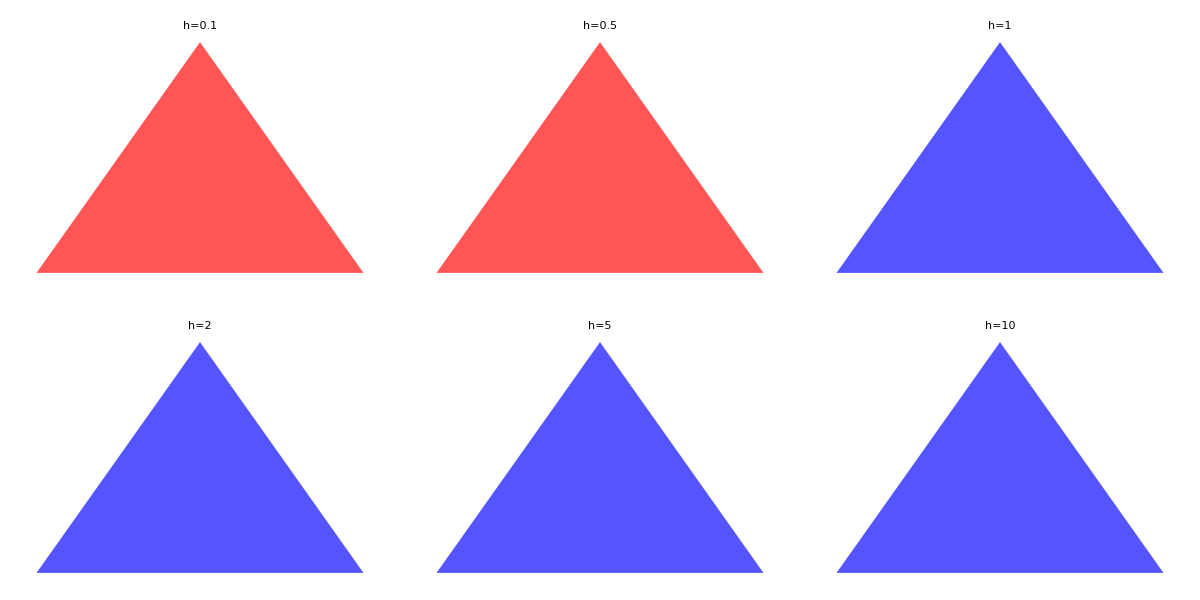
-Graphics- |

```mathematica
UltrametricQ[d_] := AllTrue[Flatten[Table[
	d[[i,j]]≤Max[{d[[i,k]], d[[k,j]]}], 
	{i, Length@d}, {j, Length@d}, {k, Length@d}]], #==True&]
triangle[h_] := {{-1/2, 0}, {1/2,0}, {0, h}}

umcolor[h_]:=Piecewise[{{Lighter@Blue, UltrametricQ[dmtx[h]]}, {Lighter@Red, ¬UltrametricQ[dmtx[h]]}}]
isoscelesfig = Grid[{{Grid[ArrayReshape[Table[Graphics[{umcolor[h], 
	Triangle[triangle[h]]}, 
	PlotLabel->Style["h="<>ToString[h], Black], 
	ImageSize->Tiny], 
	{h, {0.1, 0.5, 1, 2, 5, 10}}], {2, 3}]], 
	SwatchLegend[Lighter@{Red, Blue}, {"Non-Ultrametric", "Ultrametric"}]}}]
```

One problem that this causes with the numbers equivalent RQE is that heterogeneity increases with h when the distance function is not ultrametric, but the relationship changes when the distance function becomes ultrametric. We show this in the plot below.

```mathematica
neqrqefig = Legended[Show[
	Plot3D[NeqRQEultra[h, θ],{θ, 0, 1/3}, {h, 0, (√3)/2}, 
			PlotStyle->Lighter@Red, AxesLabel->Automatic],
	Plot3D[NeqRQEultra[h, θ],{θ, 0, 1/3}, {h, (√3)/2, 3}, 
			PlotStyle->Lighter@Blue, AxesLabel->Automatic],
PlotLabel->Style["Numbers Equivalent RQE", Black], AxesStyle->Black], 
SwatchLegend[Lighter/@{Red, Blue}, {"Non-Ultrametric", "Ultrametric"}]]
```

-Graphics3D-

It is left as an exercise to show that the numbers equivalent RQE in this case is maximized  at the transition point from an ultrametric to a non-ultrametric distance, which here is at h=√(3/4).

## B.3. Functional Hill Numbers

Chiu & Chao (2014) introduced the functional Hill numbers of order q ,  for which they first presented a generalized RQE which they then normalize by Q_1:

```mathematica
Subscript[F, q] = (Subscript[Q, q]/Subscript[Q, 1])^(1/(2(1-q)))
```

((∑_(i=1)^n ∑_(j=1)^n (p_i p_j)^q d_(i,j))/(∑_(i=1)^n ∑_(j=1)^n p_i p_j d_(i,j)))^(1/(2 (1-q)))

Their derivation is an enjoyable exercise worth reading for those interested. Unfortunately, when the abundance distribution is perfectly even, their measure always yields the observed richness n, which is easy to prove directly:

```mathematica
b3expr = Subscript[F, q] /. {Subscript[p, i]->1/n, Subscript[p, j]->1/n}
```

((∑_(i=1)^n ∑_(j=1)^n (1/n^2)^q d_(i,j))/(∑_(i=1)^n ∑_(j=1)^n (d_(i,j))/n^2))^(1/(2 (1-q)))

```mathematica
b3expr = b3expr /. {(∑_(i=1)^n ∑_(j=1)^n (1/n^2)^q Subscript[d, i,j])/(∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j]/n^2)->n^(2(1-q))(∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j])/(∑_(i=1)^n ∑_(j=1)^n Subscript[d, i,j])}
PowerExpand@b3expr
```

(n^(2 (1-q)))^(1/(2 (1-q)))

n

□

The above problem, and one other, can be observed in the following example. Consider a parameterized distance matrix

```mathematica
dmtx[h]//MatrixForm
```

(0 | 1 | √(1/4+h^2)
1 | 0 | √(1/4+h^2)
√(1/4+h^2) | √(1/4+h^2) | 0)

and probability distribution,

```mathematica
prob[θ]
```

{1/3,1/3+θ,1/3-θ}

which gives the following formula for the functional Hill numbers.

```mathematica
pp[θ_]:=prob[θ]⊗prob[θ]
dpp[h_, θ_]:=dmtx[h]pp[θ]
FuncHillultra[q_][h_, θ_]:=Piecewise[{{(Total[Total[dmtx[h](prob[θ]⊗prob[θ])^q]]/(prob[θ].dmtx[h].prob[θ]))^(1/(2(1-q))), q≠1}, {ⅇ^(-Total[Total[dpp[h,θ]/(2Total[Total[dpp[h,θ]]])Log[pp[θ]]]]), q==1}}]
```

We can use this to observe some properties of F_q graphically (here we use the q=1 setting).

```mathematica
funchillfig = Legended[Show[
	Plot3D[FuncHillultra[1][h, θ],{θ, 0, 1/3}, {h, 0, (√3)/2}, 
			PlotStyle->Lighter@Red, AxesLabel->Automatic],
	Plot3D[FuncHillultra[1][h, θ],{θ, 0, 1/3}, {h,(√3)/2,3}, 
			PlotStyle->Lighter@Blue, AxesLabel->Automatic, 
			PlotRange->Full] ,
	Plot3D[3,{θ, 0, 1/3}, {h, 0, 3}, Mesh->None, 
			ColorFunction->Function[{x, y, z},Opacity[0.6, Gray]]], 
PlotLabel->Style["F_1", Black], AxesStyle->Black], 
SwatchLegend[Lighter/@{Red, Blue}, {"Non-Ultrametric", "Ultrametric"}]]
```

-Graphics3D-

We observe the property in which F_q=3 whenever all probabilities are equal (here 1/3). Another concern is that under the ultrametric regime, the F_q first increases with progressively greater inequality in the abundance distribution, before decreasing again at the extremes of inequality. However, in the non-ultrametric region, the gradient is steepest with respect to the abundance distribution, rather than the distance metric. Therefore, F_q shows different behaviour under non-ultrametric and ultrametric distance functions, and in general may be more sensitive to abundance inequality than dissimilarity. This could be of a particular concern when the categories over which abundance is measured are ill-defined or unreliable.

## B.4. The Leinster-Cobbold Index

The Leinster-Cobbold index L_q is defined as

```mathematica
Subscript[L, q]=(∑_(i=1)^n Subscript[p, i]^q(∑_(j=1)^n Subscript[Z, i,j] Subscript[p, i])^(1-q))^(1/(1-q));
```

where Z is an n×n similarity matrix (Leinster & Cobbold, 2012). A similarity matrix can be expressed in terms of the distance matrix D in several ways. Leinster and Cobbold used the transformation Z_(i,j)=e^(-u D_(i,j)), where u is a scaling factor. When u=1,  Z_(i,j)=1 everywhere. Conversely, when u→∞, Z_(i,j)=1 and one can easily verify L_q becomes the Rényi heterogeneity in that case.

```mathematica
sim[h_, u_:1] := Exp[-u dmtx[h]]; 
sim[h]//MatrixForm
```

(1 | 1/ⅇ | ⅇ^(-√(1/4+h^2))
1/ⅇ | 1 | ⅇ^(-√(1/4+h^2))
ⅇ^(-√(1/4+h^2)) | ⅇ^(-√(1/4+h^2)) | 1)

```mathematica
LCIultra[q_][h_,θ_,u_:1]:=Piecewise[{{(prob[θ].(sim[h, u].prob[θ])^(q-1))^(1/(1-q)), q≠1}, {Product[((sim[h, u].prob[θ])^(-prob[θ]))[[i]],{i, 3}], q==1}}]
```

The following plots show a couple of the issues with the L_q index.

```mathematica
lcifig = Grid[{Flatten@{Table[Show[
	Plot3D[LCIultra[1][h, θ, u],{θ, 0, 1/3}, {h, 0, (√3)/2}, 
			PlotStyle->Lighter@Red, AxesLabel->Automatic],
	Plot3D[LCIultra[1][h, θ, u],{θ, 0, 1/3}, {h,  (√3)/2,3}, 
			PlotStyle->Lighter@Blue, AxesLabel->Automatic] , 
PlotLabel->Style["LCI (q=1)\n" Superscript["Z_(i,j)=ⅇ", "-"<>ToString[u]<>"D_(i,j)"], Black], 
PlotRange->{Automatic, Automatic, {1, 3}}, AxesStyle->Black,
GridLines->Automatic], {u, {0, 1, 5}}], {SwatchLegend[Lighter/@{Red, Blue}, {"Non-Ultrametric", "Ultrametric"}]}}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- |

Namely, that it is particularly sensitive to the form with which the similarities are computed. As we increase the factor u, the maximal value of the L_q gradually approaches 3. However, as it does so, it appears to progressively lose sensitivity to distance. Since distances are often easier to compute than similarities, this may be a problem.  

Another problem is that one only truly reaches the categorical Rényi heterogeneity when u→∞. This can be proven  L_q as h→∞.

```mathematica
lcilimit = Limit[FullSimplify@PowerExpand@LCIultra[1][h, θ,u], h->∞];
lcilimit = FullSimplify[lcilimit, Assumptions->{θ<1/3, u>0, ⅇ^u (1+3 θ)>-1}]
```

(3 ⅇ^(u (2/3+θ)) (1-3 θ)^(-1/3+θ) (1+ⅇ^u (1+3 θ))^(-1/3-θ))/((1+ⅇ^u+3 θ)^(1/3))

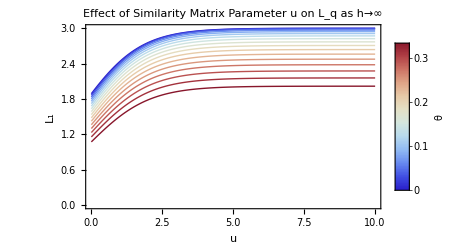

```mathematica
Themes`AddThemeRules["abestheme",
DefaultPlotStyle->Thread@Directive[Darker[#]&/@{Blue, Red, Green, Magenta, Cyan, Orange},Thick],
LabelStyle->Directive[Black, 13, FontFamily-> "Times New Roman"],
Frame->True, 
FrameStyle->Directive[Black, 13, FontFamily->"Times New Roman"]];

lcilimitplot = Legended[
ListLinePlot[Table[
	{u, lcilimit}, 
	{θ, 0, 1/3, 0.02}, {u, 0, 10, 0.1}],
AxesLabel->{"u", "L_1"},
PlotLabel->"Effect of Similarity Matrix Parameter u on L_q as h→∞",
PlotTheme->"abestheme",
PlotStyle->"ThermometerColors"], 
BarLegend[{"ThermometerColors",{0,1/3}}, LegendLabel->"θ"]]
```

This plot shows that (as expected) the LCI will asymptotically approach a limiting value as u increases. However, the limiting value will depend on category abundance inequality θ. 

Next, we show that in the limit of both h→∞ and u→∞, the upper bound on L_q decreases as a function of θ over the range [0, 1/3).

```mathematica
lcilimithu = FullSimplify[
		Limit[lcilimit, u->∞], 
	Assumptions->{θ<1/3, u>0, ⅇ^u (1+3 θ)>-1}]
```

3 (1-3 θ)^(-1/3+θ) (1+3 θ)^(-1/3-θ)

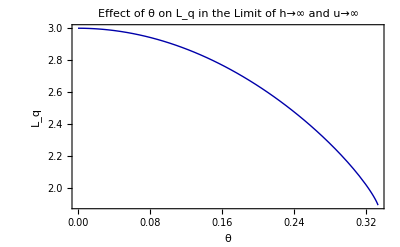

```mathematica
Plot[lcilimithu, {θ, 0, 1/3}, AxesLabel->{"θ", "L_q"}, 
PlotTheme->"abestheme",
PlotLabel->"Effect of θ on L_q in the Limit of h→∞ and u→∞"]
```

We can also show that 3 (1-3 θ)^(-1/3+θ) (1+3 θ)^(-1/3-θ) is an upper bound on L_q in the limit of h→∞. We do this by showing that

∂_u (lim_(h→∞, u→∞) L_q-lim_(h→∞) L_q) <0

for finite u. First we compute the difference of the limit expressions.

```mathematica
dlimit = FullSimplify[
	lcilimithu-lcilimit, 
	Assumptions->{θ<1/3, u>0, ⅇ^u (1+3 θ)>-1}]
```

3 (1-3 θ)^(-1/3+θ) ((1+3 θ)^(-1/3-θ)-(ⅇ^(u (2/3+θ)) (1+ⅇ^u (1+3 θ))^(-1/3-θ))/((1+ⅇ^u+3 θ)^(1/3)))

The result then follows from some simple algebraic manipulations.

```mathematica
dlimexpr = FullSimplify@D[ExpandAll@dlimit, u] < 0
```

-(ⅇ^(u (2/3+θ)) (1+ⅇ^u) (1-3 θ)^(-1/3+θ) (2+9 θ (1+θ)) (1+ⅇ^u (1+3 θ))^(-4/3-θ))/((1+ⅇ^u+3 θ)^(4/3))<0

```mathematica
dlimexpr = FullSimplify@ApplySides[(# ((1+ⅇ^u+3 θ)^(4/3)))/(ⅇ^(u (2/3+θ)) (1+ⅇ^u))&, dlimexpr]
```

(1-3 θ)^(1/3+θ) (2+9 θ (1+θ)) (1+ⅇ^u (1+3 θ))^(2/3+θ)>0

```mathematica
dlimexpr = FullSimplify@ApplySides[#/((1-3 θ)^(1/3+θ)(1+ⅇ^u (1+3 θ))^(2/3+θ)) &, dlimexpr]
```

2+9 θ (1+θ)>0

```mathematica
dlimexpr = ApplySides[(# - 2)/9&, dlimexpr]
```

θ (1+θ)>-2/9

```mathematica
FullSimplify[dlimexpr, Assumptions->{0≤θ<1/3}]
```

True

□

The implications of this result are non-trivial. They ostensibly mean that the Leinster-Cobbold index will only reach true comparability with the Rényi heterogeneity when (dis)similarity is completely ignored (i.e. when the u parameter of the similarity function reaches ∞).

## C. Numbers Equivalent Meta-Analytic Heterogeneity

In meta-analysis (DerSimonian & Laird, 1986), one is given a vector of observed effect sizes, y=(y_i)_(i=1)^n, and variances v=(σ_i^2)_(i=1)^n for n studies. The effects are assumed to be generated under a hierarchical model depicted in the figure below.

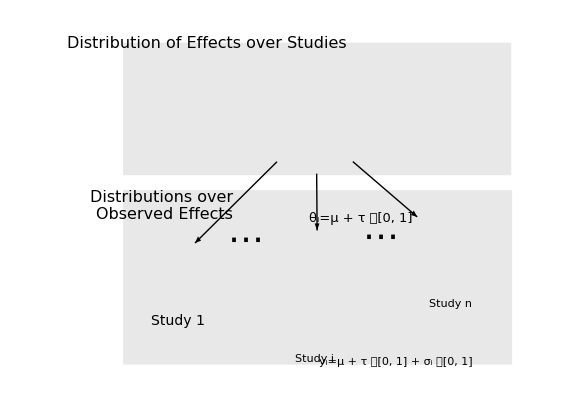

The ith study’s observed effect size, y_i, is assumed to be normally distributed with mean θ_i and variance σ_i^2. The study means θ=(θ_i)_(i=1)^n are in turn assumed to be normally distributed with “true” mean μ (the “summary effect”) and variance τ^2, which is the dispersion in study effects.

Estimation of μ, τ^2, and θ, their statistical significance, and heterogeneity proceeds as follows. This is largely based on the

Statistic | Formula | Index
Study weight | w_i=1/σ_i^2 | (1)
Weighted mean effect | ȳ=(∑_(i=1)^n w_i y_i)/(∑_(j=1)^n w_j) | (2)
Cochran's Q | Q=∑_(i=1)^n (w_i(y_i-ȳ))^2 | (3)
Degrees of freedom | ν=n-1 | (4)
Scaling factor | γ=∑_(i=1)^n w_i-((∑_(j=1)^n w_j^2)/(∑_(k=1)^n w_k)) | (5)
Study heterogeneity | τ^2=Piecewise[{{1/γ(Q - ν), Q>ν}, {0, Q≤ν}}] | (6)
Combined weights | w_i^*=1/(σ_i^2+τ^2) | (7)
Combined variance | v_i^*=1/w_i^* | (8)
Pooled effect | (ȳ)^*=(∑_(i=1)^n w_i^*y_i)/(∑_(j=1)^n w_j^*) | (9)
Standardized effect | Z^*=(ȳ)^*/(√(σ_i^2+τ^2)) | (10)
One tailed p-value | p_1=1-Φ[Z^*] | (11)
Two tailed p-value | p_2=2(1-Φ[|Z^*|]) | (12)
Between study entropy | H[τ]=1/2 Log[2 π ⅇ τ^2] | (13)
Rényi heterogeneity (q=1) | Π_1[τ]=ⅇ^(-1/2Log[2 π ⅇ τ^2]) | (14)

### Function implementations

```mathematica
Tmean[w_, T_]:=(∑_(i=1)^Length[w] w[[i]]T[[i]])/(∑_(j=1)^Length[w] w[[j]])
CochranQ[w_, T_]:=∑_(i=1)^Length[w] w[[i]](T[[i]]-Tmean[w, T])^2
DoF[T_] := Length[T]-1
ExcessVariance[w_, T_]:= CochranQ[w,T]-DoF[T]
ScalingFactor[w_]:=(∑_(i=1)^Length[w] w[[i]])-((∑_(j=1)^Length[w] w[[j]]^2)/(∑_(k=1)^Length[w] w[[k]]))
TauSquared[w_, T_]:=Piecewise[{{(CochranQ[w, T]-DoF[T])/ScalingFactor[w], CochranQ[w, T]>DoF[T]}, {0, CochranQ[w, T]≤DoF[T]}}]
CombinedWeights[v_, τ2_]:=1/(v + τ2)  
CombinedVariance[w_]:=1/(∑_(i=1)^Length[w] w[[i]]) 
CombinedStandardError[v_]:=√v
ConfidenceInterval95[Tmean_, SE_]:= {Tmean - 1.96 SE, Tmean + 1.96 SE}
ZScore[Tmean_, SE_]:=Tmean/SE 

pvalue[Z_, tails_:2]:=Piecewise[{{SurvivalFunction[NormalDistribution[], Z], tails==1}, {2 SurvivalFunction[NormalDistribution[], Abs[Z]], tails==2}}]
```

### (Pseudo)Forest plot implementation

```mathematica
ForestPlot:=Function[{T, V,nullpoint, studynames, title, xlabel}, 
	Module[{W, data, sizelist},
		W = 1/V;
		data = Table[{T[[i]], i}, {i, 1, Length@T}];
		sizelist = Table[0.2 W[[i]]/Total[W], {i, 1, Length@T}];
		errplot =ListPlot[Table[{Around[T[[i]], Sqrt@V[[i]]], i}, {i,1 , Length@T}], PlotStyle->{Black}];
		dotplot=Graphics[Table[{PointSize[sizelist[[i]]], Black,Point[data[[i]]]}, {i,1 , Length@T}]];
		nullplot = ListLinePlot[{{nullpoint, nullpoint}, {0, Length@W+1}}, PlotStyle->Directive[Red, Dashed]];
		Show[errplot,nullplot, dotplot, 
		PlotLabel->Style[title, Black, 16],
		Frame->True, FrameStyle->Directive[Black,16],
		FrameLabel->{xlabel, None},
		FrameTicks-> {Automatic, Table[{i, studynames[[i]]}, {i, Length@T}], None, None}]]
]
```

## C.1. Test Example

Consider the following set of studies:

```mathematica
effects = {0.3, 0.1, 0.4, 0.63, 0.22, 0.19, 0.7, -0.1};
variances = {0.01, 0.03, 0.05, 0.05, 0.05, 0.02, 0.01, 0.06};
weights = 1/variances;
```

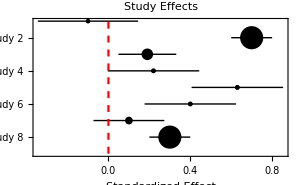
-Graphics- |  | Effect Size | Variance | Weight
Study 8 | 0.3 | 0.01 | 100.
Study 7 | 0.1 | 0.03 | 33.33
Study 6 | 0.4 | 0.05 | 20.
Study 5 | 0.63 | 0.05 | 20.
Study 4 | 0.22 | 0.05 | 20.
Study 3 | 0.19 | 0.02 | 50.
Study 2 | 0.7 | 0.01 | 100.
Study 1 | -0.1 | 0.06 | 16.67

```mathematica
effectstable = TextGrid[Transpose[{
Flatten[{"", Table[Style["Study "<>ToString[i], Bold], 
					{i, Length@effects, 1, -1}]}],
Flatten[{Style["Effect Size", Bold],effects}], 
Flatten[{Style["Variance", Bold],variances}], 
Flatten[{Style["Weight", Bold],Round[weights, 0.01]}]
}], Frame->All];

forestplot = Show[ForestPlot[effects, 
variances, 0, 
Table["Study "<>ToString[i], {i,Length@effects,1,-1}],
"Study Effects", 
"Standardized Effect"], ImageSize->300];

metaanalysisgrid = Grid[{{forestplot, effectstable}}]
```

The traditional estimates are shown here:

```mathematica
tau = √TauSquared[weights, effects]
```

0.218872

```mathematica
combinedweights = CombinedWeights[variances, tau^2];
summaryeffect = Tmean[combinedweights, effects]
```

0.325376

```mathematica
combinedvar = CombinedVariance[combinedweights];
combinedSE = CombinedStandardError[combinedvar]
```

0.0990092

```mathematica
ci95 = ConfidenceInterval95[summaryeffect, combinedSE]
```

{0.131318,0.519434}

```mathematica
zscore = ZScore[summaryeffect, combinedSE]
"One tailed p-value="<>ToString[N@pvalue[zscore, 1]]
"Two tailed p-value="<>ToString[N@pvalue[zscore, 2]]
```

3.28632

One tailed p-value=0.000507525

Two tailed p-value=0.00101505

The following figure demonstrates the accuracy of this method based on 50 simulation runs of an 8-study meta-analysis for increasing values of τ in the range 0.01 to 10. One can appreciate that the estimation generally falls along the line of perfect estimation in that figure.

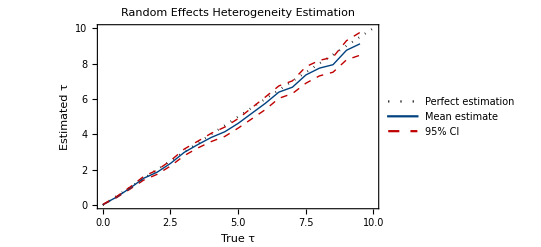

```mathematica
(* Functions for the simulation *)
𝒩[μ_:0, σ_:1] := NormalDistribution[μ, σ]
P[μ_,τ_,σ_]:=TransformedDistribution[μ + τ η + σ ϵ, {η \[Distributed] 𝒩[], ϵ \[Distributed] 𝒩[]}]
Π[τ_]:=√(2 ⅇ π) τ
SampleEffects[μ_, τ_, v_] := Table[
	RandomVariate[P[μ, τ, √v[[j]]]],  
	{j, 1, Length[v]}]
SimEstimationTau[μ_, τ_, v_]:= Function[n, 
	Module[{S, SE, meanS},
		S = Table[Sqrt[
				TauSquared[Table[1/v[[i]],{i, 1, Length@v}], 
				SampleEffects[μ, τ, v]]], {j, 1, n}];
		SE = StandardDeviation[S]/√n;
		meanS = Mean[S];
		{meanS - 1.96 SE, meanS, meanS + 1.96 SE}
]]
SimEstimationRenyi[μ_, τ_, v_]:= Function[n, 
	Module[{S, SE, R, meanR},
		S = Table[Sqrt[
			TauSquared[Table[1/v[[i]],{i, 1, Length@v}], 
			SampleEffects[μ, τ, v]]], {j, 1, n}];
		R = Table[Π[S[[i]]], {i, 1, Length@S}];
		SE = StandardDeviation[R]/√n;
		meanR = Mean[R];
		{meanR - 1.96 SE, meanR, meanR + 1.96 SE}
]]

(*Runs the simulation*)
simres = Table[
	{τ, SimEstimationTau[0.5, τ, variances][100]}, 
	{τ, 0.01, 10, 0.5}];
m = Table[{simres[[i]][[1]], simres[[i]][[2, 2]]}, {i, 1, Length[simres]}];
lci = Table[{simres[[i]][[1]], simres[[i]][[2, 1]]}, {i, 1, Length[simres]}];
uci = Table[{simres[[i]][[1]], simres[[i]][[2, 3]]}, {i, 1, Length[simres]}];
diag = Table[{i, i}, {i, 0, 10, 0.01}];

(* Plot the results *)
actualestimateplot = Show[
	ListLinePlot[{diag, lci, m, uci}, 
		PlotStyle->{{Black, Dotted},
				   {ColorData[81][3], Dashed, Thick},
				   {ColorData[81][1], Thick},  
				   {ColorData[81][3], Dashed, Thick}}, 
	Frame->True, FrameStyle->Directive[Black, 16], 
	FrameLabel->{"True τ", "Estimated τ"}, 
	PlotLegends->Placed[
		LineLegend[{Directive[Black, Dotted],
					Directive[ColorData[81][1], Thick],  
					Directive[ColorData[81][3], Dashed, Thick]}, 
					{"Perfect estimation", "Mean estimate", "95% CI"}],
		{0.3, 0.7}]], 
	PlotLabel->Style["Random Effects\nHeterogeneity Estimation", Black, 16]]
```

## C.2. The Effective Number of Study Effects

Generally, the above estimates are used to adjust the study weights and average effect to compute the statistical significance of the summary effect. However, we will diverge from the usual treatment of random-effects meta-analysis to now demonstrate how its heterogeneity estimate can be converted to numbers equivalent. Simply put, one notes that τ^2 is the variance of a normal distribution, whose Shannon entropy is defined as H[τ]=1/2 Log[2 π ⅇ τ^2], and whose corresponding Rényi heterogeneity is Π_1[τ]=ⅇ^(-1/2Log[2 π ⅇ τ^2]). For the same system simulated above, we show the corresponding Rényi heterogeneity below. This would correspond to the “effective number of study effects”

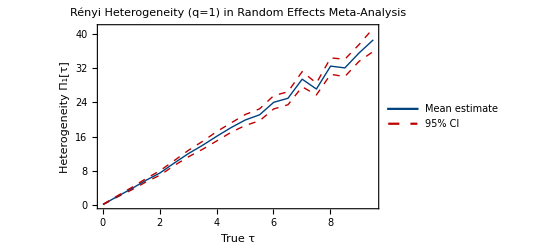

```mathematica
simrenyi = Table[
	{τ, SimEstimationRenyi[0.5, τ, variances][100]}, 
	{τ, 0.01, 10, 0.5}];
m = Table[{simrenyi[[i]][[1]], simrenyi[[i]][[2, 2]]}, 
	{i, 1, Length[simrenyi]}];
lci = Table[{simrenyi[[i]][[1]], simrenyi[[i]][[2, 1]]}, 
	{i, 1, Length[simrenyi]}];
uci = Table[{simrenyi[[i]][[1]], simrenyi[[i]][[2, 3]]}, 
	{i, 1, Length[simrenyi]}];

mixedeffrenyifig = Show[ListLinePlot[
	{lci, m, uci}, 
	PlotStyle->{{ColorData[81][3], Dashed, Thick},
				{ColorData[81][1], Thick},  
				{ColorData[81][3], Dashed, Thick}}, 
Frame->True, FrameStyle->Directive[Black, 16], 
FrameLabel->{"True τ", "Heterogeneity Π_1[τ]"}, 
PlotLegends->Placed[
	LineLegend[{Directive[ColorData[81][1], Thick],  
				Directive[ColorData[81][3], Dashed, Thick]}, 
				{"Mean estimate", "95% CI"}],{0.3, 0.7}]
], PlotLabel->Style[
	"Rényi Heterogeneity (q=1)\nin Random Effects Meta-Analysis", 
	Black, 16]]
```

One possible criticism of this approach is the fact that the Shannon differential entropy for a continuous distribution is not a mere continuous extension of the discrete Shannon entropy. Indeed, the differential entropy can at times be negative, which should not occur for a true entropy. To this end, Jaynes (1963) showed that the appropriate extension is known as the limiting density of discrete points. Interestingly, this does not pose much of a problem for numbers equivalent heterogeneity measurements since both continuous and discrete forms are measuring the size of a distribution’s base of support (Cover & Thomas, 2006).

### C.2.1 Variance Violates the Axiom of Replication

One may also question why numbers equivalent would be more useful than simply reporting the variance-based meta-analytic heterogeneity index. To this end, we appeal once again to the replication principle. The replication principle effectively states that if we combine n equally heterogeneous systems with non-overlapping bases of support (i.e. event spaces), then the heterogeneity of the pooled system should be n-fold larger than the heterogeneity of any single constituent. If we use variance as the heterogeneity measure, the replication principle will be violated. Let us use a simple example with uniform distributions. Consider having n uniform distributions on the intervals,

(γ = {[γ_(i-1), γ_i)})_(i=1)^n∩{[γ_(n-1), γ_n]}

In our implementation of this here, we will simply assume n=4

```mathematica
intervals[n_] := Flatten[{Table[{Subscript[γ, i-1], Subscript[γ, i]}, {i,1, n-1}], {{Subscript[γ, n-1], Subscript[γ, n]}}}, 1]
```

where (γ_i-γ_(i-1))=(γ_(j-1)-γ_j) ∀(i,j)∈{1,2,...,n} and γ_(i-1)<γ_i ∀_i. The PDF for the i’th uniform distribution is defined on the half open interval [γ_(i-1), γ_i) as follows:

```mathematica
fhalfopen[{a_, b_}][x_] := Piecewise[{{1/(b-a), a≤x<b}, {0, True}}]
HalfOpenUniform[{a_, b_}]:=ProbabilityDistribution[
	fhalfopen[{a, b}][x], 
	{x, -∞, ∞}]
```

Pooling uniform distributions defined on the intervals in Equation 5 result in the following mixture distribution:

```mathematica
pweight[γ_] := Table[1/(Length[γ]-1), Length[γ]]
unifdist[γ_, i_] := Piecewise[{{HalfOpenUniform[{γ[[i,1]], γ[[i,2]]}], i<Length[γ]}, {UniformDistribution[{γ[[i,1]], γ[[i,2]]}], i==Length[γ]}}]

umixdist[γ_] := MixtureDistribution[
		pweight[γ], 
	Table[unifdist[γ, i], {i, 1, Length[γ]}]]
```

```mathematica
mixpdf = FullSimplify[PDF[umixdist[intervals[4]], x], 
	Assumptions->{Subscript[γ, 0]<Subscript[γ, 1]<Subscript[γ, 2]<Subscript[γ, 3]<Subscript[γ, 4], Not[x<Subscript[γ, 1]&& x≥Subscript[γ, 2]]}
]
```

Piecewise[{{1/(4 (-γ_0+γ_1)), x≥γ_0&&x<γ_1}, {1/(4 (-γ_1+γ_2)), x≥γ_1&&x<γ_2}, {1/(4 (-γ_2+γ_3)), x≥γ_2&&x<γ_3}, {1/(4 (-γ_3+γ_4)), x≥γ_3&&x≤γ_4}, {0, True}}]

The pooled pmf will be 1/(γ_K-γ_0) since (γ_k-γ_(k-1))=(γ_K-γ_0)/4:

```mathematica
mixpdf /. Table[(Subscript[γ, k]-Subscript[γ, k-1])->(Subscript[γ, 4]-Subscript[γ, 0])/4, {k, 1, 4}]
```

Piecewise[{{1/(-γ_0+γ_4), (x≥γ_0&&x<γ_1)||(x≥γ_1&&x<γ_2)||(x≥γ_2&&x<γ_3)||(x≥γ_3&&x≤γ_4)}, {0, True}}]

The following plot depicts an example of these distributions.

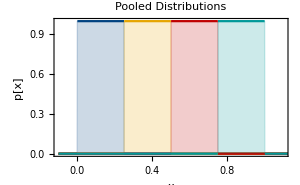
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* This first function constructs an array of these distributions*)
b = Range[0, 1, 0.25];
phou= Table[HalfOpenUniform[{b[[i]], b[[i+1]]}], {i, 1, Length[b]-1}];
unifdistfig = Grid[ArrayReshape[{
	Table[Plot[PDF[phou[[i]], x], {x,-0.1, 1.5},
	PlotLabel->Style[
		"𝒰["<>ToString[b[[i]]]<>","<>ToString[b[[i+1]]]<>"]", 
		Black],
	Frame->True, FrameStyle->Directive[Black], 
	FrameLabel-> {"x", "p[x]"},
	PlotRange->{{-0.1, 1.1}, Automatic},
 PlotStyle-> ColorData[81][i], Filling->Axis, 
 ImageSize->125], 
 {i, 1, Length@phou}]}, 
{2, 2}]];

pooleddistfig = Show[Table[
	Plot[1/4 PDF[phou[[i]], x], 
	{x,-0.1, 1.5}, PlotRange->{{-0.1, 1.1}, Automatic},
	PlotStyle-> ColorData[81][i], Filling->Axis], 
	{i, 1, Length@phou}], 
Frame->True, FrameStyle->Directive[Black], 
FrameLabel-> {"x", "p[x]"}, 
PlotLabel->Style["Pooled Distributions", Black], 
ImageSize->300];


unifdistgrid = Grid[{{pooleddistfig, unifdistfig}}]
```

The variance for the uniform distribution on the half-open interval is the same as that of the uniform distribution on the closed interval:

```mathematica
halfovar = FullSimplify[
	Variance[HalfOpenUniform[{Subscript[γ, i-1], Subscript[γ, i]}]], 
Assumptions->{Subscript[γ, i]-Subscript[γ, i-1]>0}]
```

1/12 (γ_(-1+i)-γ_i)^2

```mathematica
closedvar = FullSimplify[
	Variance[UniformDistribution[{Subscript[γ, i-1], Subscript[γ, i]}]], 
Assumptions->{Subscript[γ, i]-Subscript[γ, i-1]>0}] /. Subscript[γ, -1+i]-Subscript[γ, i] -> Subscript[γ, i]-Subscript[γ, -1+i]
```

1/12 (-γ_(-1+i)+γ_i)^2

Thus, the pooled variance will be as follows:

```mathematica
pooledvar = Variance[UniformDistribution[{Subscript[γ, 0], Subscript[γ, n]}]]
```

1/12 (-γ_0+γ_n)^2

If we assume that the variance is a heterogeneity measure, it would satisfy the following equality under the axiom of replication:

```mathematica
rpunifvar = pooledvar == n closedvar
```

1/12 (-γ_0+γ_n)^2==1/12 n (-γ_(-1+i)+γ_i)^2

but simply rearranging shows us that it does not. Since |γ_n-γ_0|=K|γ_i-γ_(i-1)|, we have the following:

```mathematica
rpunifvar = rpunifvar /. (Subscript[γ, n]-Subscript[γ, 0])-> n (Subscript[γ, i]-Subscript[γ, i-1])
```

1/12 n^2 (-γ_(-1+i)+γ_i)^2==1/12 n (-γ_(-1+i)+γ_i)^2

```mathematica
rpunifvar = ApplySides[(# 12)/(-Subscript[γ, -1+i]+Subscript[γ, i])^2 &, rpunifvar]
```

n^2==n

```mathematica
TrueQ[rpunifvar]
```

False

However, we can show that the continuous version of the Rényi heterogeneity,

Π_q[p]=(∫p[x]^q ⅆx),

does satisfy the axiom of replication. The Rényi heterogeneity of the uniform distribution is

```mathematica
unifhet = (∫_Subscript[γ, i-1]^Subscript[γ, i] (Subscript[γ, i]-Subscript[γ, i-1])^-q ⅆx)^(1/(1-q));
unifhet = FullSimplify@PowerExpand@unifhet
```

-γ_(-1+i)+γ_i

which conveniently describes the exact size of the base of support for the uniform model. We can now easily see that the replication principle will be satisfied.

```mathematica
repunifrenyi = (∫_Subscript[γ, 0]^Subscript[γ, n] (Subscript[γ, n]-Subscript[γ, 0])^-q ⅆx)^(1/(1-q)) == n (∫_Subscript[γ, i-1]^Subscript[γ, i] (Subscript[γ, i]-Subscript[γ, i-1])^-q ⅆx)^(1/(1-q))
```

((-γ_0+γ_n)^(1-q))^(1/(1-q))==n ((-γ_(-1+i)+γ_i)^(1-q))^(1/(1-q))

```mathematica
repunifrenyi = PowerExpand@repunifrenyi
```

-γ_0+γ_n==n (-γ_(-1+i)+γ_i)

```mathematica
repunifrenyi = repunifrenyi /. (Subscript[γ, n]-Subscript[γ, 0])-> n (Subscript[γ, i]-Subscript[γ, i-1])
```

True

### C.2.2. Numbers Equivalent of Between-Study Effects

We can now compute the Rényi heterogeneity of Gaussian distributed between-study effects. This requires us to compute the following integral:

Π_q[τ] = ((2 π)^(-q/2) τ^-q∫ ⅇ^(-(q (θ-μ)^2)/(2 τ^2)) ⅆθ)^(1/(1-q)),

which is that of the Gaussian pdf raised to the power q.

```mathematica
indefint = PowerExpand@Integrate[PDF[NormalDistribution[μ, τ], θ]^q, θ];
lim[x_, l_] := Limit[x, l, Assumptions->{q>0, τ>0}]
defint = (lim[indefint, θ->∞] - lim[indefint, θ->-∞])^(1/(1-q));
defint = FullSimplify@PowerExpand@defint
```

√(2 π) q^(1/(2 (-1+q))) τ

We also want to compute the limit as q→1,

```mathematica
defint1 = Limit[defint ,q->1]
```

√(2 ⅇ π) τ

and as q→∞.

```mathematica
defintinf = Limit[defint, q->∞]
```

√(2 π) τ

The Rényi heterogeneity is thus

```mathematica
renyinorm[q_][τ_]:= Piecewise[{{√(2 π) q^(1/(2 (-1+q))) τ, q≠1}, {√(2 ⅇ π) τ, q==1}, {√(2 π) τ, q==∞}}]
```

If one estimates τ^2 using the DerSimonian & Laird method, one can then compute the “effective  total number of study effects” using the above form for Rényi heterogeneity. At q=1, this would be the “effective number of typical study effects” whereas at q=2, one would have the effective “total number of common study effects,” and so forth.  The value of τ is computed as follows:

Showing that continuous uniform distributions satisfy the replication principle was relatively simple, since we can set those distributions up to have disjoint domains. However, all univariate Gaussians defined on the real line will have overlapping domains, so the proof becomes more difficult. Here, we simply show that the replication principle can be satisfied for two univariate Gaussians.

Recall that the Rényi heterogeneity has the following decomposition:

```mathematica
Clear[Π]
decompeq = Subscript[Π, q,γ] == Subscript[Π, q,α] Subscript[Π, q,β]
```

Π_(q,γ)==Π_(q,α) Π_(q,β)

For 2 univariate Gaussians with equal heterogeneity (and thus equal variance σ^2), the between study effect standard deviation τ is

```mathematica
τ = Sqrt[TauSquared[Table[{1/σ^2}, 2], Table[Subscript[y, i], {i, 2}]]];
τ = FullSimplify@Extract[τ, {1,1,1,1,1}]
```

1/2 (-2 σ^2+(y_1-y_2)^2)

pooled heterogeneity (where for simplicity we here assume that q=1) is

```mathematica
Subscript[Π, q,γ] = renyinorm[q][τ]
```

Piecewise[{{√(π/2) q^(1/(2 (-1+q))) (-2 σ^2+(y_1-y_2)^2), q≠1}, {√((ⅇ π)/2) (-2 σ^2+(y_1-y_2)^2), q==1}, {√(π/2) (-2 σ^2+(y_1-y_2)^2), q==∞}, {0, True}}]

The within-study (α) heterogeneity is as follows:

```mathematica
Subscript[Π, q,α] = ((√(2 π) q^(1/(2 (-1+q)))(∑_(i=1)^M Subscript[w, i]^q Subscript[σ, i]))/(∑_(j=1)^M Subscript[w, j]^q))^(1/(1-q))
```

(2 π)^(1/(2 (1-q))) ((q^(1/(2 (-1+q))) ∑_(i=1)^M w_i^q σ_i)/(∑_(j=1)^M w_j^q))^(1/(1-q))

We take the limit as q→1 to obtain the value for Π_(1,α). First, we move into log space and rearrange terms.

```mathematica
ralphalim1 = ExpandAll@PowerExpand@Log[((√(2 π) q^(1/(2 (-1+q)))(∑_(i=1)^M Subscript[w, i]^q Subscript[σ, i]))/(∑_(j=1)^M Subscript[w, j]^q))^(1/(1-q))]
```

Log[2]/(2-2 q)+Log[π]/(2-2 q)+Log[q]/((1-q) (-2+2 q))-Log[∑_(j=1)^M w_j^q]/(1-q)+Log[∑_(i=1)^M w_i^q σ_i]/(1-q)

```mathematica
ralphalim1 = ralphalim1 /. Log[q]/((1-q) (-2+2 q))-> 1/(1-q)Log[q^(1/(-2+2 q))]
```

Log[2]/(2-2 q)+Log[π]/(2-2 q)+Log[q^(1/(-2+2 q))]/(1-q)-Log[∑_(j=1)^M w_j^q]/(1-q)+Log[∑_(i=1)^M w_i^q σ_i]/(1-q)

Now we apply L’Hopital’s rule to each term.

(Log[2]/(2-2 q))_term1+(Log[π]/(2-2 q))_term2+(Log[q^(1/(-2+2 q))]/(1-q))_term3-(Log[∑_(j=1)^n w_j^q]/(1-q))_term4+(Log[∑_(i=1)^n w_i^q σ_i]/(1-q))_term5

```mathematica
fracdiff[x_, v_]:=D[Numerator[x], v]/D[Denominator[x], v]
fraclim[x_, v_, l_]:=Limit[Numerator[x], v->l]/Limit[Denominator[x], v->l]
lhopital[x_, v_, l_]:=Limit[D[Numerator[x], v]/D[Denominator[x], v], v->l]
term1 = lhopital[Log[2]/(2-2 q), q, 1];
term2 = lhopital[Log[π]/(2-2 q), q, 1];
term3 = lhopital[Log[q^(1/(-2+2 q))]/(1-q),q,1];
term4 =fracdiff[Log[∑_(j=1)^M Subscript[w, j]^q]/(1-q),q]/.{ 
	(∑_(j=1)^M Log[Subscript[w, j]] Subscript[w, j]^q)/(∑_(j=1)^M Subscript[w, j]^q)->(∑_(j=1)^M Limit[Log[Subscript[w, j]] Subscript[w, j]^q,q->1])/(∑_(j=1)^M Limit[Subscript[w, j]^q,q->1])};
term5 = fracdiff[Log[∑_(i=1)^M Subscript[w, i]^q Subscript[σ, i]]/(1-q),q]/.{
	-(∑_(i=1)^M Log[Subscript[w, i]] Subscript[w, i]^q Subscript[σ, i])/(∑_(i=1)^M Subscript[w, i]^q Subscript[σ, i])->-(∑_(i=1)^M Limit[Log[Subscript[w, i]] Subscript[w, i]^q Subscript[σ, i],q->1])/(∑_(i=1)^M Limit[Subscript[w, i]^q Subscript[σ, i],q->1])};
ralphalim1 = term1 + term2 + term3 + term4 + term5
```

1/4-(∑_(j=1)^M Log[w_j] w_j)/(∑_(j=1)^M w_j)-(∑_(i=1)^M Log[w_i] w_i σ_i)/(∑_(i=1)^M w_i σ_i)

The final expression for Π_(1,α) is thus:

```mathematica
Subscript[Π, 1,α] = Exp@PowerExpand[ralphalim1 /. {Subscript[w, i]->1/σ^2, Subscript[w, j]->1/σ^2, Subscript[σ, i]->σ}]
```

ⅇ^(1/4) σ^4

where the study weights are used. The between-study (β) heterogeneity is thus

```mathematica
Subscript[Π, 1,β] = (renyinorm[1][τ])/Subscript[Π, 1,α] //FullSimplify
Subscript[Π, 2,β] =(renyinorm[2][τ])/(Subscript[Π, q,α]/.{q->2, Subscript[w, i]->1/σ^2, Subscript[w, j]->1/σ^2, Subscript[σ, i]->σ})
```

(ⅇ^(1/4) √(π/2) (-2 σ^2+(y_1-y_2)^2))/σ^4

2 π σ (-2 σ^2+(y_1-y_2)^2)

How separated do the distributions have to be in order to show that Π_(q,β)=2? We solve for δ=|y_1-y_2| at Π_(q,β)=2 to yield the following relationships. First we express the β-heterogeneity in terms of δ:

```mathematica
renyibeta[q_][σ_, δ_] := 
	Piecewise[{{(ⅇ^(1/4) √(π/2) (-2 σ^2+ δ^2))/σ^4, q==1}, {2^(-(-2+q)/(2 (-1+q))) π^(q/(2 (-1+q))) q^(q/(2 (-1+q)^2)) σ^(-1+q/(-1+q)) (-2 σ^2+δ^2), q≠1}}]
```

```mathematica
res = PowerExpand@Table[Extract[FullSimplify[
Solve[2 ==renyibeta[q][σ, δ], δ]], {2, 1, 2}], {q, {1/1000,1/2,1, 2, 3}}]
```

{√2 √(2 2^(1333/665334) 5^(500/332667) π^(1/1998) σ^(1000/999)+σ^2),√(2+8 √(2 π)) σ,√2 √(σ^2+(√(2/π) σ^4)/ⅇ^(1/4)),(√(1+2 π σ^3))/(√π √σ),√((2 2^(1/4))/(3^(3/8) π^(3/4) √σ)+2 σ^2)}

The distance between y_1 and y_2 required to have a β-Rényi heterogeneity of 2 across different values of σ is shown in the following plot:

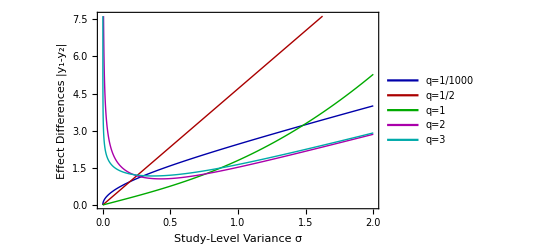

```mathematica
Plot[res, {σ, 0, 2}, 
PlotRange->Automatic,
PlotTheme->"abestheme", 
FrameLabel->{"Study-Level Variance σ", "Effect Differences |y_1-y_2|"}, 
PlotLegends->{"q=1/1000", "q=1/2", "q=1", "q=2", "q=3"}]
```

The above plot makes some interesting points. First, we note that at q=1/2, the distance required between distributions to satisfy the replication principle is linear in the standard deviation (√(2+8 √(2 π))σ). Secondly, as the q>1, we observe convexity such that the intercept is no longer 0. At face value, this does not seem appropriate: intuition suggests that as the variances between studies becomes smaller, the difference in their means required to become “effectively categorical” should gradually approach 0. 

The particularly interesting aspect of Π_q^β as a measure of between-study heterogeneity is not only that it can satisfy the replication principle, but that its units are the effective number of completely distinct study effects. 

At this stage, our presentation of meta-analytic heterogeneity in the units of numbers equivalent was merely to show that this expression is possible. We are not advocating for its wider adoption at this point in time, since there are further properties that should be investigated. Namely, in the continuous domain, the heterogeneity can decrease below 1, the implications of which should be further examined. Moreover, the meaning of this heterogeneity statistic at different values of q (especially above and below 0) could warrant further investigation.

## References

Chiu CH, Chao A. Distance-based functional diversity measures and their decomposition: A framework based on hill numbers. PLoS ONE. 2014;9(7).
Chao A, Chiu C-H, Jost L. Unifying Species Diversity, Phylogenetic Diversity, Functional Diversity, and Related Similarity and Differentiation Measures Through Hill Numbers. Annu Rev Ecol Evol Syst. 2014;45(1):297–324. 
Cover TM, Thomas JA. Elements of information theory. 2nd ed. Hoboken, N.J: Wiley-Interscience; 2006. 748 p.
DerSimonian R, Laird N. Meta-analysis in clinical trials. Control Clin Trials. 1986;7(3):177–188.
Jaynes ET. Information Theory and Statistical Mechanics. In: Statistical Physics [Internet]. New York, NY: W.A. Benjamin, Inc.; 1963. p. 182–218. Available from: https://bayes.wustl.edu/etj/articles/brandeis.pdf
Jost L. Partitioning Diversity into Independent Alpha and Beta Components. Ecology. 	2007;88(10):2427–2439.
Leinster T, Cobbold CA. Measuring diversity: The importance of species similarity. Ecology. 2012;93(3):477–489.
Rao CR. Diversity and dissimilarity coefficients: A unified approach. Theor Popul Biol. 1982;21(1):24–43.
Ricotta C, Szeidl L. Diversity partitioning of Rao’s quadratic entropy. Theor Popul Biol. 2009;76(4):299–302.
Tsallis C. Possible generalization of Boltzmann-Gibbs statistics. J Stat Phys. 1988;52(1–2):479–487.
Walker B, Kinzig A, Langridge J. Plant Attribute Diversity, Resilience, and Ecosystem Function: The Nature and Significance of Dominant and Minor Species. Ecosystems. 1999 Mar 1;2(2):95–113.